## Prerequisites: Helper functions

First, we will declare a set of basic functions that will become useful later. Notice the use of the “:=” operator here to tell Mathematica that while labels[x] has some definite value, that value should not be computed until labels[x] is needed (later in the program). In particular, whatever value labels[] is called with will be used as symbol “x” (x_ is a named placeholder) and then the right side of the assignment will be evaluated. In other words, it’s a function.

```mathematica
SetDirectory[NotebookDirectory[](* This is important so that saved files go the right place*)]; 

(* Don't worry about these two lines too much. They are unnecessarily complicated and don't do much important. I had to use Google to figure them out. *)
labels[x_]:=Transpose[x/.Rule->List][[1]]
eqns[x_]:=Transpose[x/.Rule->List][[2]]
```

makeGrid[] builds a nicely-formatted grid by first making a list with one row for each of the desired columns, then Transposing that list to columns, then using Grid[] to get a nicely formatted output, which is then Rasterized to an image. Notice that all builtin objects start with capital letters, and all the ones I declare myself begin with lowercase so I can tell them apart. To figure out what a function does (like Map, for example), click it and press “F1” on your keyboard.

```mathematica
makeGrid[names_, equations_, plots_] := Grid[Transpose[{names, Map[TraditionalForm,equations], plots}], Frame->All]
```

## Problem 6: Explicit functions

First, we declare the inputs of the system, a list of named equations we are interested in analyzing.

```mathematica
explicitFuncs = {"Constant"->0,"Linear"->x,"Quadratic"->x^2,"Cubic"->x^3,"Sine"->Sin[x],"Inverse Sine"->ArcSin[x],"Tangent"->Tan[x],"Inverse tangent"->ArcTan[x],"Positive exponential"->E^x,"Negative exponential"->E^(-x),"Log"->Log[x]};
```

Next, we generate a plot for each of the input functions. Table[] is the “for each” part here, making a table of the value of “Plot[i, ...]” for each value of i in eqns[explicitFunctions]

```mathematica
explicitPlots = Table[Plot[i,{x,0,10}, PlotTheme->"Web"], {i,eqns[explicitFuncs]}];
```

Finally, we export those results in a nice grid, using the helper function makeGrid defined at the top. Because it starts with a lowercase letter, it must be a function we defined ourselves.

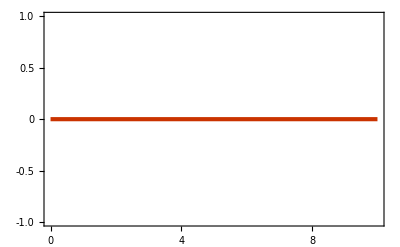
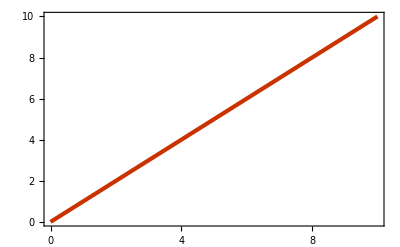
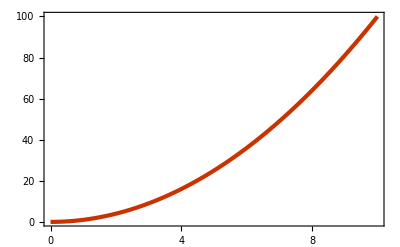
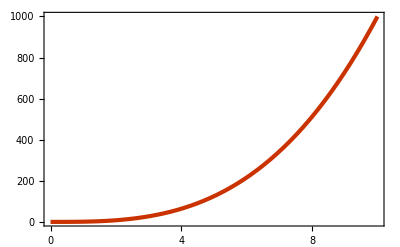
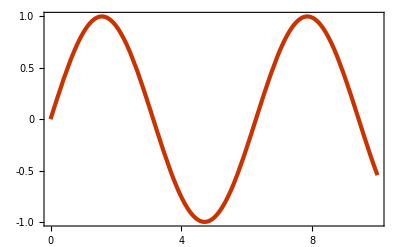
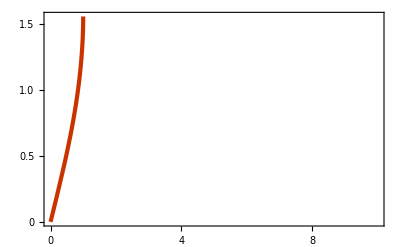
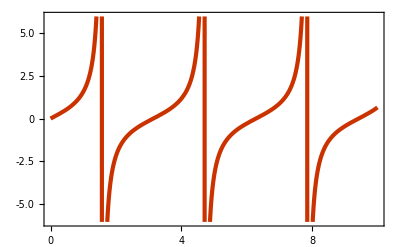
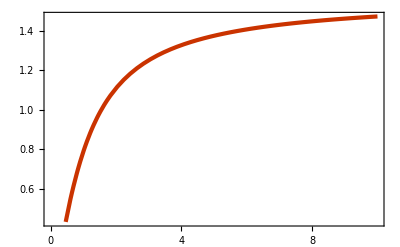
Constant | f(x)==0 | -Graphics-
Linear | f(x)==x | -Graphics-
Quadratic | f(x)==x^2 | -Graphics-
Cubic | f(x)==x^3 | -Graphics-
Sine | f(x)==sin(x) | -Graphics-
Inverse Sine | f(x)==sin^-1(x) | -Graphics-
Tangent | f(x)==tan(x) | -Graphics-
Inverse tangent | f(x)==tan^-1(x) | -Graphics-
Positive exponential | f(x)==ⅇ^x | -Graphics-
Negative exponential | f(x)==ⅇ^-x | -Graphics-
Log | f(x)==log(x) | -Graphics-

Table 1.png

```mathematica
export1 = makeGrid[labels[explicitFuncs], Table[f[x]==i,{i,eqns[explicitFuncs]}], explicitPlots]
Export["Table 1.png",export1]
```

### Hint: Double-click the rightmost blue bar (with the arrow) to show a section

## Problem 8: Conic Sections

```mathematica
conicFunctions = {"Circle"-> x^2+y^2-4,"Ellipse" -> x^2+3y^2-9, "Parabola" -> x^2-y, "Hyperbola" -> y^2-x^2-1};
```

```mathematica
conicPlots = Table[ContourPlot[i==0,{x,-5,5}, {y,-5,5}, PlotTheme->"Web"], {i,eqns[conicFunctions]}];
```

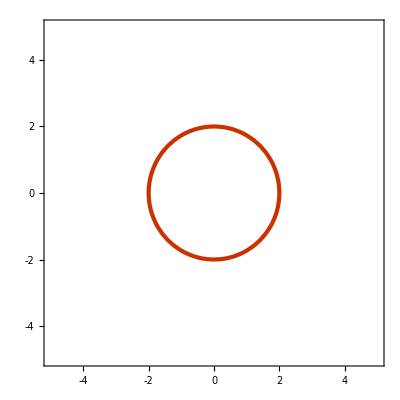
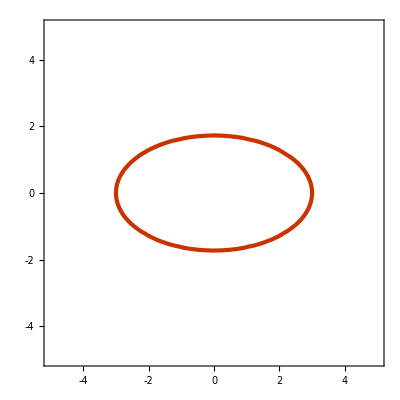
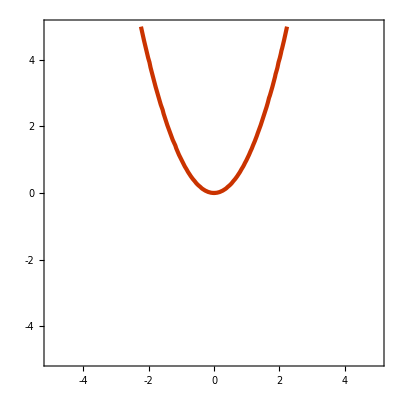
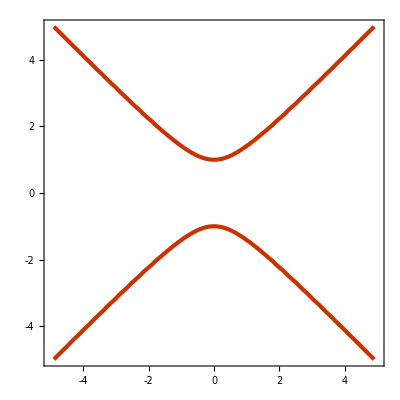
Circle | x^2+y^2-4==0 | -Graphics-
Ellipse | x^2+3 y^2-9==0 | -Graphics-
Parabola | x^2-y==0 | -Graphics-
Hyperbola | -x^2+y^2-1==0 | -Graphics-

Table 2.png

```mathematica
export2 = makeGrid[labels[conicFunctions], Table[i==0, {i,eqns[conicFunctions]}],conicPlots]
Export["Table 2.png",export2]
```

## Problem 11: Quadratic Surfaces

```mathematica
surfaceFunctions = {"Plane" -> x, "Elipsoid" -> 2 x^2 + y^2 + 3z^2 - 16,"One-sheet Hyperboloid"-> x^2 + y^2 - z^2-4, "Hyperbolic Parabaloid" ->3 x^2 - 3y^2 +10 z};
```

```mathematica
surfacePlots = Table[ContourPlot3D[i==0,{x,-5,5}, {y,-5,5}, {z,-5,5}], {i,eqns[surfaceFunctions]}];
```

```mathematica
export3 = makeGrid[labels[surfaceFunctions], Table[i==0, {i,eqns[surfaceFunctions]}],surfacePlots]
Export["Table 3.png",export3];
```

Plane | x==0 | -Graphics3D-
Elipsoid | 2 x^2+y^2+3 z^2-16==0 | -Graphics3D-
One-sheet Hyperboloid | x^2+y^2-z^2-4==0 | -Graphics3D-
Hyperbolic Parabaloid | 3 x^2-3 y^2+10 z==0 | -Graphics3D-

## Problems 12/13: Implicitly defining an apple

Some serious guesswork was used here, but hopefully you can see my process, at least a little. First, I played around with making some ovals, then figured out how to revolve those into torus-like things, then exported the result to a file. Manipulate[] (remember, F1 for an explanation) is a useful tool here.

```mathematica
Manipulate[ContourPlot[x^2+i(y-i2)^2==1,{x,-1,1},{y,-1,1}],{i,0.6,1.8}, {i2,0,1}]
```

```mathematica
Manipulate[ContourPlot3D[z^2 + i(Sqrt[x^2+y^2]-i2)^2 ==1, {x,-2,2},{y,-2,2},{z,-2,2}],{i,0.6,1.8}, {i2,0,1}]
```

Playing with the manipulate sliders let me discover that (1.4, 0.7) was a resonable set of values. Here they are plugged in.

```mathematica
appleFunction := z^2 + 1.4(Sqrt[x^2+y^2]-.7)^2
Print[TraditionalForm[appleFunction==1]]
export = ContourPlot3D[appleFunction==1, {x,-1.6,1.6},{y,-1.6,1.6},{z,-1.6,1.6}]
Export["Apple.png", Rasterize[export, RasterSize -> 800]];
```

1.4 (√(x^2+y^2)-0.7)^2+z^2==1

-Graphics3D-

## Problem 7: Functions of real world contours

#### Apple

```mathematica
ImageCompose[-Graphics-,ContourPlot[x^2+y^2==.6,{x,-1,1},{y,-1,1}]]
Image[ImageCompose[-Graphics-,Show[Plot[Sqrt[1-x^2],{x,-1,1}],PlotRegion->{{0, 1}, {.5, .9}}]],ImageSize->Medium]
```

-Graphics-

#### Provided function

```mathematica
f[x_,y_]:=x^2+x y+y^2-x-y-1
```

```mathematica
(*f[x_,y_]:= Norm[{2,1}*RotationMatrix[1].{x,y}]-1*)
```

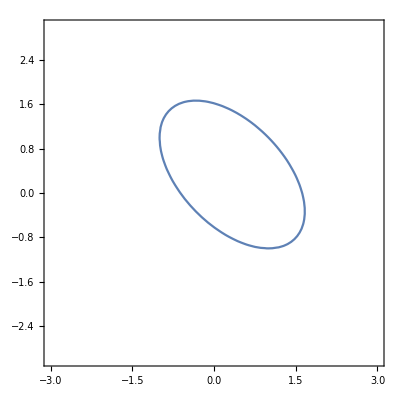

```mathematica
ContourPlot[f[x,y]==0,{x,-3,3},{y,-3,3}]
```